```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
dirName="/home/dan/ResearchLocal/adiabatic"
SetDirectory[dirName];
```

/home/dan/ResearchLocal/adiabatic

```mathematica
fontweight="Bold"; fontsize=12;
exportPlot[name_]:=Export[StringJoin[StringJoin[dirName,"/",name,".pdf"]],ToExpression[name]]
```

## Cos temp profile setup

```mathematica
au=1.496*10^13;rc=115 au;rcInAu=115;nz=10*8;mpiz=2;zMax=4;
```

### Define reference parameters

```mathematica
Tatm0=40;
Tmid0=19;
zq0=2.0;
```

### Define how the parameters scale with r (relative to the reference parameters)

```mathematica
Tmid[r_]:=Tmid0(r/(200 au))^-0.5;
Tatm[r_]:=Tatm0(r/(155 au))^-0.3;
zq[r_]:=63au(r/(200 au))^1.3*Exp[-(r/(800au))^2];
δ[r_]:=0.0034(r/(1au)-200)+2.5;
```

### Define the temperature profile as a function of z in physical units

```mathematica
Tcos[r_,z_]:=If[Abs[z]<zq[r],Tatm[r]+(Tmid[r]-Tatm[r])(Cos[(π z)/(2zq[r])])^(2δ[r]),Tatm[r]];
```

### Convert the profile to physical units

```mathematica
kb=1.38*10^-16;mH=1.67372*10^-24;G=6.674*10^-8;Msun=1.988435*10^33;
Mstar=2.3*Msun;μ=2.37;
cs[r_]:=√((kb Tmid[r])/(μ mH))
Ω[r_]:=√((G Mstar)/r^3)
H[r_]:=(√2 cs[r])/Ω[r]
```

```mathematica
codeT=((Tmid[rc]+Tatm[rc])/2)/0.5;
```

```mathematica
H[rc]/rc
```

0.099129

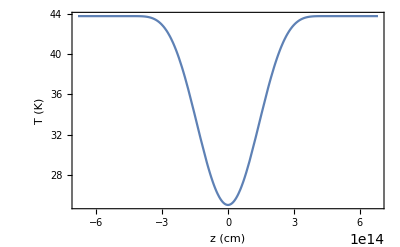

```mathematica
tempProfilePlot=Plot[Tcos[rc,z],{z,-zMax*H[rc],zMax H[rc]},Frame->True,FrameLabel->{"z (cm)","T (K)"}]
```

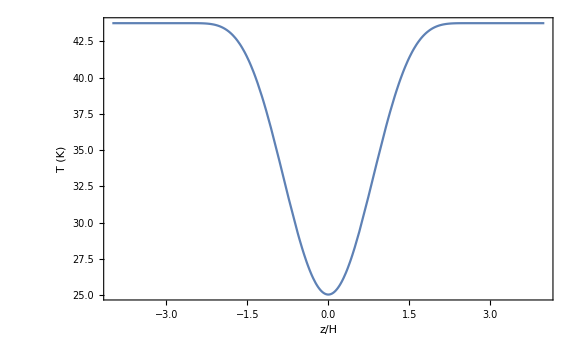

/home/dan/ResearchLocal/adiabatic/tempProfilePlot.pdf

```mathematica
TcosUnits[r_,z_]:=Tcos[r*au,z*H[r*au]]/codeT
tempProfilePlot=Plot[TcosUnits[115,z]*codeT,{z,-zMax,zMax},Frame->True,FrameLabel->{"z/H","T (K)"},BaseStyle->{FontWeight->fontweight,FontSize->fontsize},ImageSize->Large,ImagePadding->50]
exportPlot["tempProfilePlot"]
```

```mathematica
z=Table[(i-0.5)/(nz/(zMax*2))//N,{i,1,nz/2}];
```

```mathematica
P0=0.5;
sCos=NDSolve[{1/ρ1[z1] D[(TcosUnits[rcInAu,z1]*ρ1[z1]), z1]==-z1,ρ1[0]==P0/TcosUnits[rcInAu,0]},ρ1[z1],{z1,0,zMax}];
ρCos[z1_]:=Re[Evaluate[ρ1[z1]/.sCos][[1]]];
Pcos[z1_]:=ρCos[z1]*TcosUnits[rc,z1]
ρCosTab=Table[ρCos[z1],{z1,z}];
```

```mathematica
ρIsoTab=Table[Exp[-z[[i]]^2],{i,1,nz/2}];
```

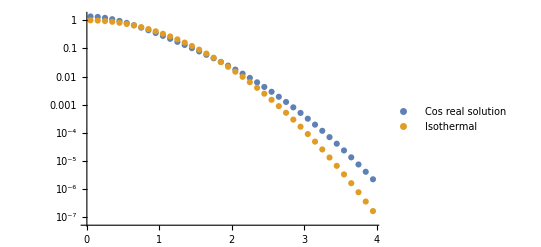

```mathematica
ListLogPlot[{Transpose[{z,ρCosTab}],Transpose[{z,ρIsoTab}]},PlotRange->Full,PlotLegends->{"Cos real solution","Isothermal"},PlotRange->Full]
```

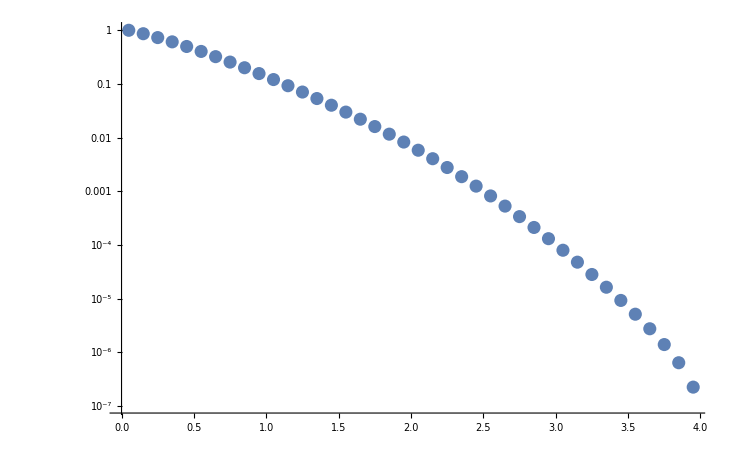

```mathematica
da=(1/10)^2;
ListLogPlot[Table[{Reverse[z][[i]],0.1*Total[Reverse[ρCosTab][[1;;i]]]},{i,1,40}]]
```

```mathematica
Tmid[rc]/codeT
Tatm[rc]/codeT
zq[rc]/H[rc]
δ[rc]
```

0.364173

0.635827

2.63655

2.211

```mathematica
zones=20^3*2*4*8;
cycles=806706;
cores=4*8*16;
seconds=20*60*60;
zones*cycles/(cores*seconds)//N
```

11204.3

```mathematica
nghost=4;ks=nghost; ke=nghost+nz-1; 
stringArray1=Table[StringJoin["pGrid->U[",ToString[k],"][js][is].d = ",ToString[AccountingForm[Reverse[ρCosTab][[k-ks+1]]]],"; \n"],{k,ks,Round[ke/2]+1}];
stringArray2=Table[StringJoin["pGrid->U[",ToString[k],"][js][is].d = ",ToString[AccountingForm[ρCosTab[[k-(ke+nghost+1)/2+1]]]],"; \n"],{k,(ke+1+nghost)/2,ke}];
StringJoin[stringArray1,stringArray2]
```

pGrid->U[4][js][is].d = 0.00000225671; 
pGrid->U[5][js][is].d = 0.00000416763; 
pGrid->U[6][js][is].d = 0.00000757654; 
pGrid->U[7][js][is].d = 0.0000135582; 
pGrid->U[8][js][is].d = 0.0000238843; 
pGrid->U[9][js][is].d = 0.0000414166; 
pGrid->U[10][js][is].d = 0.0000706994; 
pGrid->U[11][js][is].d = 0.0001188; 
pGrid->U[12][js][is].d = 0.00019651; 
pGrid->U[13][js][is].d = 0.000319988; 
pGrid->U[14][js][is].d = 0.000512909; 
pGrid->U[15][js][is].d = 0.000809325; 
pGrid->U[16][js][is].d = 0.00125712; 
pGrid->U[17][js][is].d = 0.00192218; 
pGrid->U[18][js][is].d = 0.00289324; 
pGrid->U[19][js][is].d = 0.00428701; 
pGrid->U[20][js][is].d = 0.00625406; 
pGrid->U[21][js][is].d = 0.0089849; 
pGrid->U[22][js][is].d = 0.0127176; 
pGrid->U[23][js][is].d = 0.0177465; 
pGrid->U[24][js][is].d = 0.0244335; 
pGrid->U[25][js][is].d = 0.0332232; 
pGrid->U[26][js][is].d = 0.0446625; 
pGrid->U[27][js][is].d = 0.0594251; 
pGrid->U[28][js][is].d = 0.0783422; 
pGrid->U[29][js][is].d = 0.102436; 
pGrid->U[30][js][is].d = 0.132957; 
pGrid->U[31][js][is].d = 0.171404; 
pGrid->U[32][js][is].d = 0.219534; 
pGrid->U[33][js][is].d = 0.279317; 
pGrid->U[34][js][is].d = 0.352798; 
pGrid->U[35][js][is].d = 0.441824; 
pGrid->U[36][js][is].d = 0.547563; 
pGrid->U[37][js][is].d = 0.66977; 
pGrid->U[38][js][is].d = 0.805837; 
pGrid->U[39][js][is].d = 0.949809; 
pGrid->U[40][js][is].d = 1.09179; 
pGrid->U[41][js][is].d = 1.21832; 
pGrid->U[42][js][is].d = 1.31429; 
pGrid->U[43][js][is].d = 1.36627; 
pGrid->U[44][js][is].d = 1.36627; 
pGrid->U[45][js][is].d = 1.31429; 
pGrid->U[46][js][is].d = 1.21832; 
pGrid->U[47][js][is].d = 1.09179; 
pGrid->U[48][js][is].d = 0.949809; 
pGrid->U[49][js][is].d = 0.805837; 
pGrid->U[50][js][is].d = 0.66977; 
pGrid->U[51][js][is].d = 0.547563; 
pGrid->U[52][js][is].d = 0.441824; 
pGrid->U[53][js][is].d = 0.352798; 
pGrid->U[54][js][is].d = 0.279317; 
pGrid->U[55][js][is].d = 0.219534; 
pGrid->U[56][js][is].d = 0.171404; 
pGrid->U[57][js][is].d = 0.132957; 
pGrid->U[58][js][is].d = 0.102436; 
pGrid->U[59][js][is].d = 0.0783422; 
pGrid->U[60][js][is].d = 0.0594251; 
pGrid->U[61][js][is].d = 0.0446625; 
pGrid->U[62][js][is].d = 0.0332232; 
pGrid->U[63][js][is].d = 0.0244335; 
pGrid->U[64][js][is].d = 0.0177465; 
pGrid->U[65][js][is].d = 0.0127176; 
pGrid->U[66][js][is].d = 0.0089849; 
pGrid->U[67][js][is].d = 0.00625406; 
pGrid->U[68][js][is].d = 0.00428701; 
pGrid->U[69][js][is].d = 0.00289324; 
pGrid->U[70][js][is].d = 0.00192218; 
pGrid->U[71][js][is].d = 0.00125712; 
pGrid->U[72][js][is].d = 0.000809325; 
pGrid->U[73][js][is].d = 0.000512909; 
pGrid->U[74][js][is].d = 0.000319988; 
pGrid->U[75][js][is].d = 0.00019651; 
pGrid->U[76][js][is].d = 0.0001188; 
pGrid->U[77][js][is].d = 0.0000706994; 
pGrid->U[78][js][is].d = 0.0000414166; 
pGrid->U[79][js][is].d = 0.0000238843; 
pGrid->U[80][js][is].d = 0.0000135582; 
pGrid->U[81][js][is].d = 0.00000757654; 
pGrid->U[82][js][is].d = 0.00000416763; 
pGrid->U[83][js][is].d = 0.00000225671;